## 100 nm

```mathematica
raw1=Import["/Volumes/Nachi's/VARIA Spectra/20_8_24_VARIA_100P_532_100_NOVA_Spec_OD4_Before_2.SSM"];
filename1="20_8_24_VARIA_100P_532_100_NOVA_Spec_OD4_Before_2.SSM";
raw2=Import["/Volumes/Nachi's/VARIA Spectra/20_8_24_VARIA_100P_532_100_NOVA_Spec_OD3_After.SSM"];
filename2="20_8_24_VARIA_100P_532_100_NOVA_Spec_OD3_After.SSM";
```

```mathematica
time1=Interpreter["Number"][StringTake[ToString[raw1[[2]]],11;;-2]]; (* time in ms*)
time2=Interpreter["Number"][StringTake[ToString[raw2[[2]]],11;;-2]]; (* time in ms*)
```

```mathematica
data1=Sort[raw1[[3;;]]][[40;;]];
data2=Sort[raw2[[3;;]]][[40;;]];
```

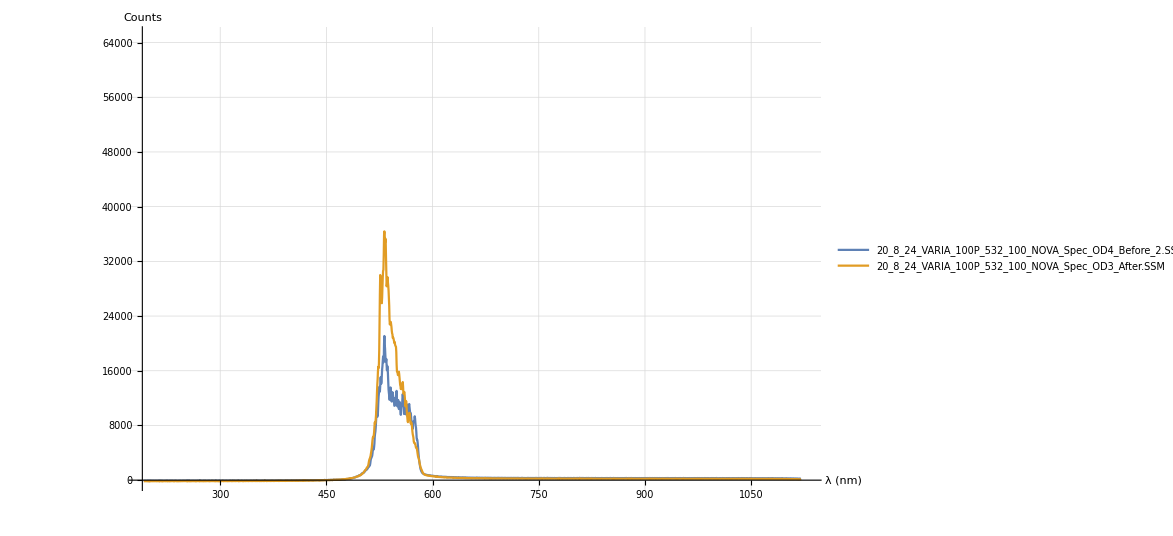

```mathematica
ListLinePlot[{data1,data2},PlotRange->{{190,1130},{-200,65000}},AxesLabel->{"λ (nm)","Counts"},GridLines->Automatic,PlotLegends->{filename1,filename2}]
```

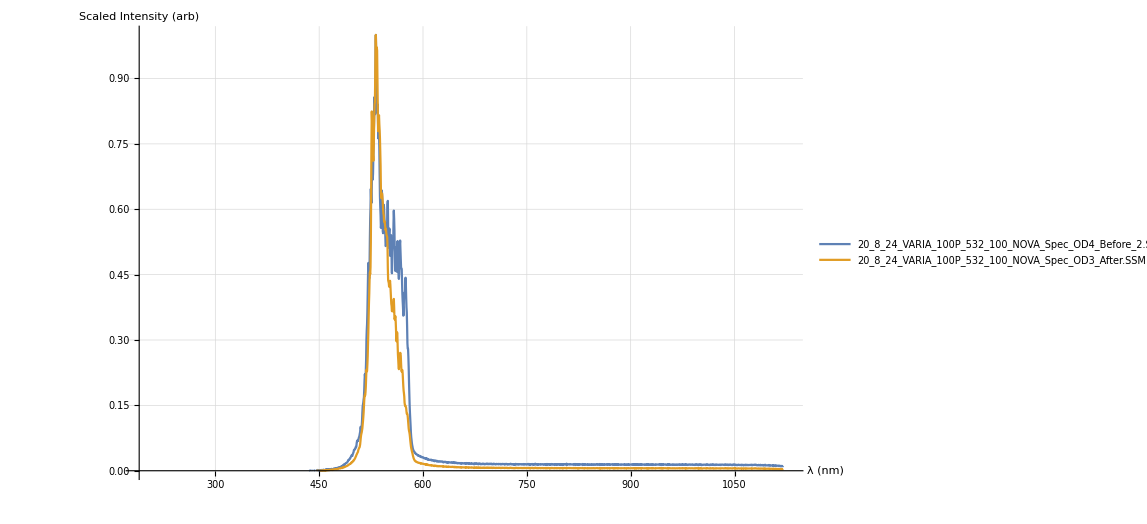

```mathematica
dataScaled1 = data1;
dataScaled1[[All,2]]=(data1[[All,2]]/Max[data1[[All,2]]]);
dataScaled2 = data2;
dataScaled2[[All,2]]=(data2[[All,2]]/Max[data2[[All,2]]]);
ListLinePlot[{dataScaled1,dataScaled2},PlotRange->{{190,1130},{0,1}},AxesLabel->{"λ (nm)","Scaled Intensity (arb)"},GridLines->Automatic,PlotLegends->{filename1,filename2}]
```

## 50 nm

```mathematica
raw1=Import["/Volumes/Nachi's/VARIA Spectra/20_8_24_VARIA_100P_532_50_NOVA_Spec_OD4_Before_02.SSM"];
filename1="20_8_24_VARIA_100P_532_50_NOVA_Spec_OD4_Before_02.SSM";
raw2=Import["/Volumes/Nachi's/VARIA Spectra/20_8_24_VARIA_100P_532_50_NOVA_Spec_OD3_After.SSM"];
filename2="20_8_24_VARIA_100P_532_50_NOVA_Spec_OD3_After.SSM";
```

```mathematica
time1=Interpreter["Number"][StringTake[ToString[raw1[[2]]],11;;-2]]; (* time in ms*)
time2=Interpreter["Number"][StringTake[ToString[raw2[[2]]],11;;-2]]; (* time in ms*)
```

```mathematica
data1=Sort[raw1[[3;;]]][[40;;]];
data2=Sort[raw2[[3;;]]][[40;;]];
```

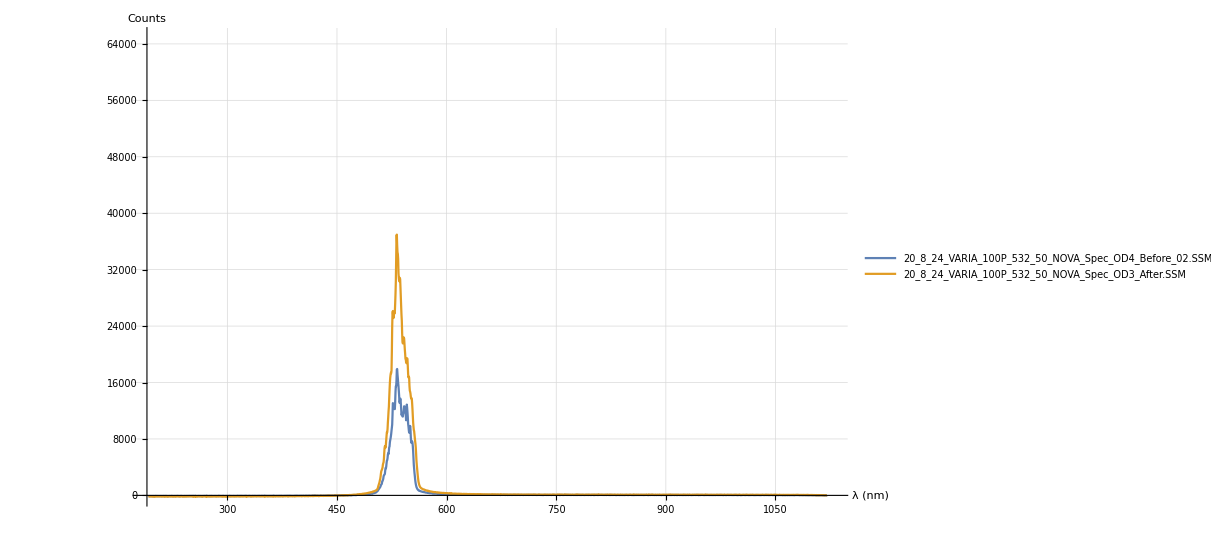

```mathematica
ListLinePlot[{data1,data2},PlotRange->{{190,1130},{-200,65000}},AxesLabel->{"λ (nm)","Counts"},GridLines->Automatic,PlotLegends->{filename1,filename2}]
```

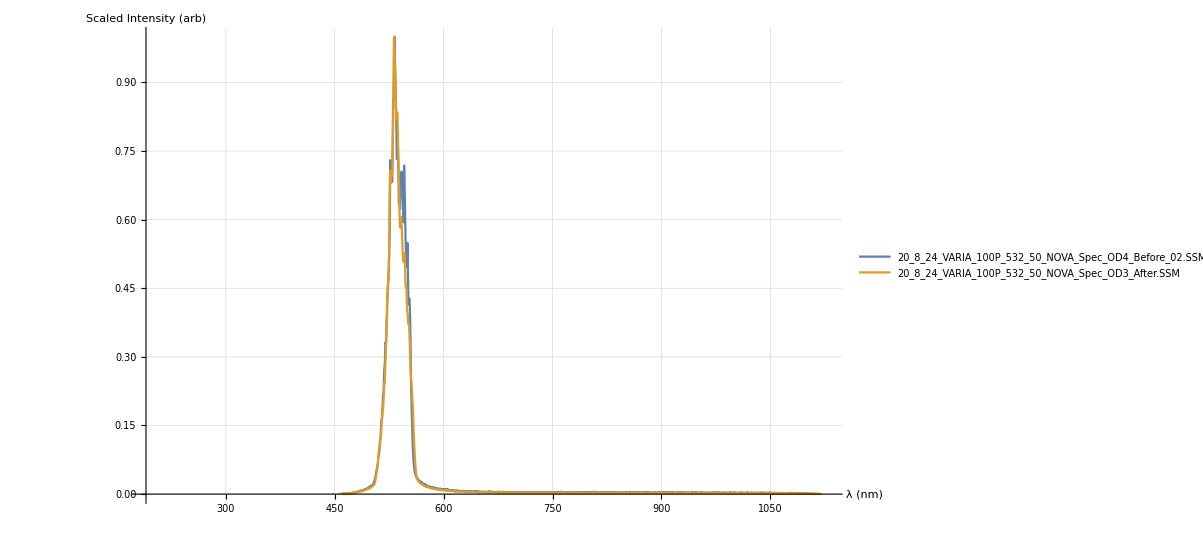

```mathematica
dataScaled1 = data1;
dataScaled1[[All,2]]=(data1[[All,2]]/Max[data1[[All,2]]]);
dataScaled2 = data2;
dataScaled2[[All,2]]=(data2[[All,2]]/Max[data2[[All,2]]]);
ListLinePlot[{dataScaled1,dataScaled2},PlotRange->{{190,1130},{0,1}},AxesLabel->{"λ (nm)","Scaled Intensity (arb)"},GridLines->Automatic,PlotLegends->{filename1,filename2}]
```

## 15 nm

```mathematica
raw1=Import["/Volumes/Nachi's/VARIA Spectra/20_8_24_VARIA_100P_532_15_NOVA_Spec_OD4_Before_2.SSM"];
filename1="20_8_24_VARIA_100P_532_15_NOVA_Spec_OD4_Before_2.SSM";
raw2=Import["/Volumes/Nachi's/VARIA Spectra/20_8_24_VARIA_100P_532_15_NOVA_Spec_OD3_After.SSM"];
filename2="20_8_24_VARIA_100P_532_15_NOVA_Spec_OD3_After.SSM";
```

```mathematica
time1=Interpreter["Number"][StringTake[ToString[raw1[[2]]],11;;-2]]; (* time in ms*)
time2=Interpreter["Number"][StringTake[ToString[raw2[[2]]],11;;-2]]; (* time in ms*)
```

```mathematica
data1=Sort[raw1[[3;;]]][[40;;]];
data2=Sort[raw2[[3;;]]][[40;;]];
```

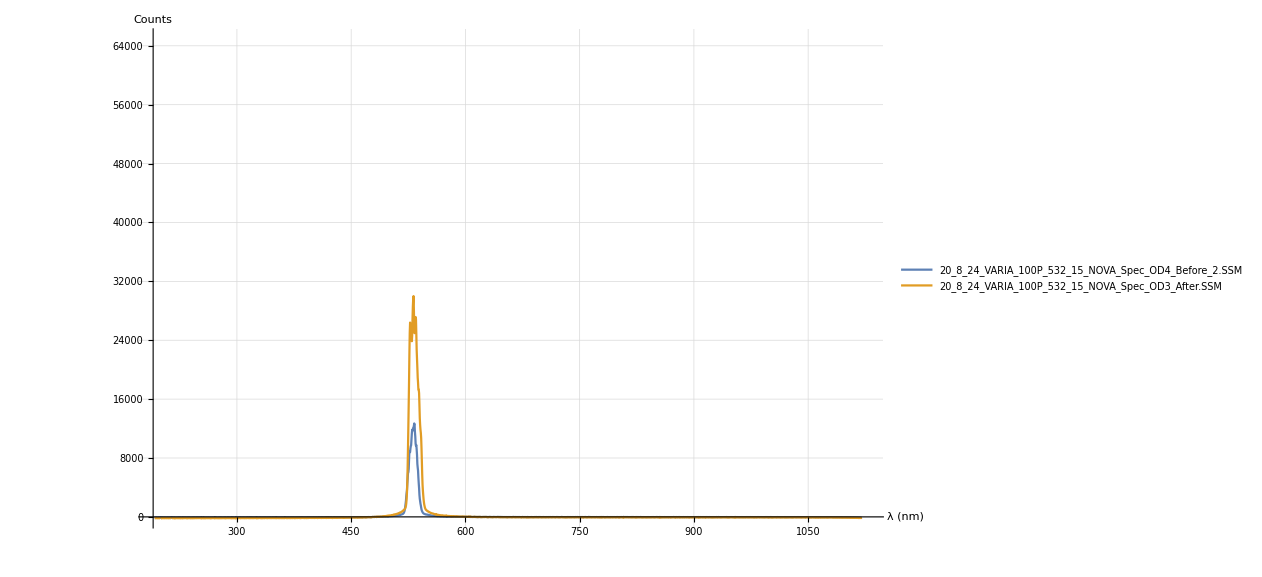

```mathematica
ListLinePlot[{data1,data2},PlotRange->{{190,1130},{-200,65000}},AxesLabel->{"λ (nm)","Counts"},GridLines->Automatic,PlotLegends->{filename1,filename2}]
```

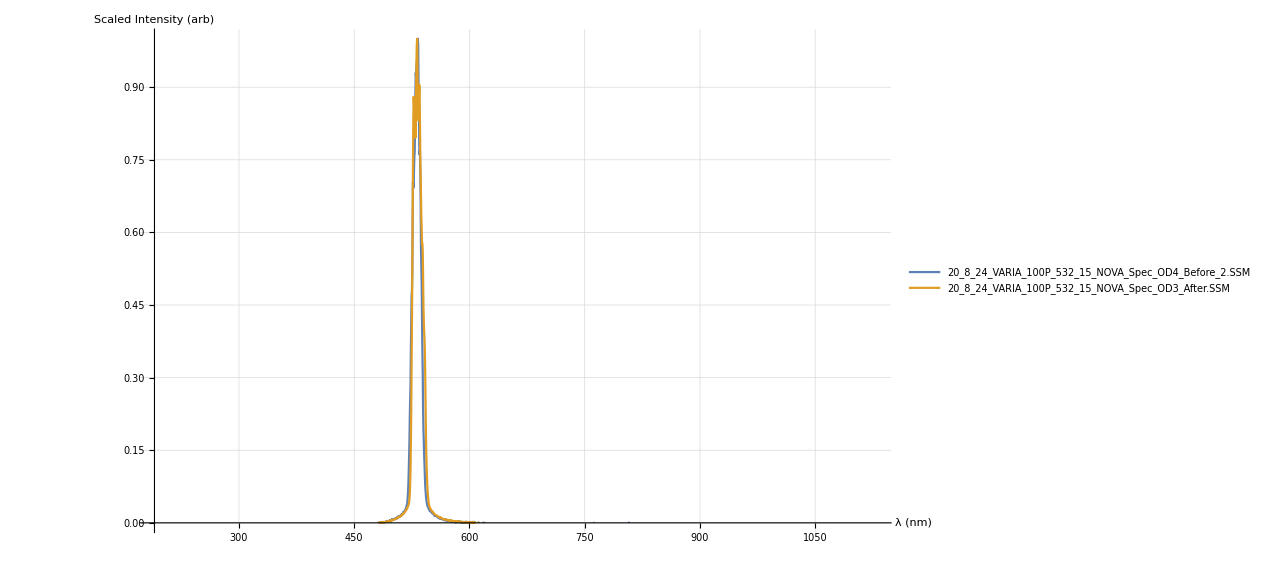

```mathematica
dataScaled1 = data1;
dataScaled1[[All,2]]=(data1[[All,2]]/Max[data1[[All,2]]]);
dataScaled2 = data2;
dataScaled2[[All,2]]=(data2[[All,2]]/Max[data2[[All,2]]]);
ListLinePlot[{dataScaled1,dataScaled2},PlotRange->{{190,1130},{0,1}},AxesLabel->{"λ (nm)","Scaled Intensity (arb)"},GridLines->Automatic,PlotLegends->{filename1,filename2}]
```